```mathematica
classicalenergy[μ_,polarization_]:=Module[{zed,length=60,intrange=6},
zed=Table[(-1)^If[Mod[n,polarization]==0,1,0],{n,1,length}];
N[Sum[Sum[If[j≠i,zed[[i]]zed[[j]]/Abs[i-j]^3,0],{j,Max[1,i-intrange],Min[length,i+intrange]}],{i,1,length}]/4.+μ Sum[zed[[i]],{i,1,length}]]/2.
]
```

```mathematica
Module[{μ=-0.1,J=0.0,bond=2,length=60,intrange=1},
newmps=MPSProductState[length,Bond->bond];
MPSNormalize[newmps];
HMatrix=Table[Table[Piecewise[{{If[α==3,μ,0.0],n==m},{If[α==3,1.0,J]/Abs[n-m]^3,Abs[n-m]≤intrange}}],{n,1,length},{m,1,length}],{α,1,3}];
{tim,energ}=AbsoluteTiming[MPSMinimizeEnergy[newmps,HMatrix,Verbose->True,InteractionRange->intrange,Sweeps->5,Tolerance->10^(-8)]];
]
```

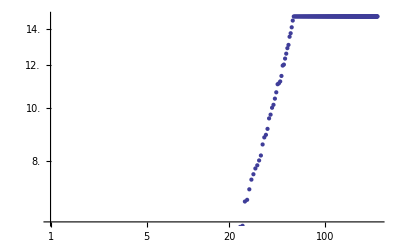

```mathematica
ListLogLogPlot[Abs[energ]]
```

```mathematica
Zvals[MPS_]:=Table[MPSExpectation[MPS,sigma[3],q],{q,1,Length[MPS],1}]
```

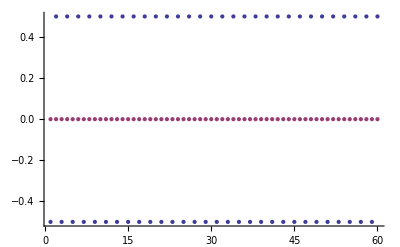

```mathematica
ListPlot[{Zvals[newmps],0 Table[(-1)^If[Mod[n,2]==0,0,1],{n,1,60}]/2},Joined->False]
```

```mathematica
Last[energ]
```

-13.294+0. ⅈ

```mathematica
Chop[classicalenergy[-0.2,2]-Last[energ]]
```

0

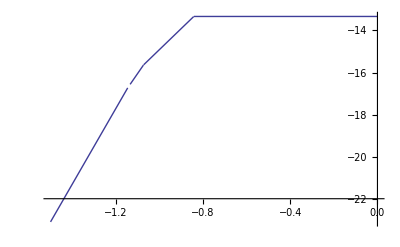

```mathematica
Plot[Min[{classicalenergy[μ,2],classicalenergy[μ,3],classicalenergy[μ,4],classicalenergy[μ,5]}],{μ,-1.5,0}]
```

```mathematica
HermitianMatrixQ[HMatrix[[3]]]
```

True

```mathematica
1/Mean[Zvals[newmps]]
```

60.

```mathematica
{Sweeps->DefaultSweeps,InteractionRange->DefaultInteractionRange,Tolerance->DefaultEnergyTolerance,MonitorEnergy->True,Verbose->False};
```

```mathematica
mps=MPSProductState[60,Bond->5];
MPSCanonize[mps]
```

0

```mathematica
{prevEnergy=0,energyList={},sweeps=2,sweep=0,IntRange=8,monitorenergy=True,tol=10^(-6),stillconverging=True,verbose=True}
```

{0,{},2,0,8,True,1/1000000,True,True}

```mathematica
mps=newmps;
```

```mathematica
numTensors=Length[mps];
```

```mathematica
(* These will be used to define left and right matrices *)
defineRight[temp_]:=Module[{fer},
ClearAll[R,fieldR,operatorsR,interactionsR];
R[numTensors+1]={{1}};
R[n_]:=R[n]=RProduct[mps[[n]],mps[[n]],R[n+1]];
fieldR[numTensors+1]=Table[{{0}},{α,1,3}];
fieldR[n_]:=fieldR[n]=Table[
RProduct[mps[[n]],mps[[n]],fieldR[n+1][[α]]]+HMatrix[[α,n,n]]RProduct[sigma[α].mps[[n]],mps[[n]],R[n+1]],{α,1,3}];
operatorsR[numTensors+2]=Table[{},{α,1,3}];
operatorsR[numTensors+1]=Table[{},{α,1,3}];
operatorsR[n_]:=operatorsR[n]=Table[
Prepend[RProduct[mps[[n]],mps[[n]],#]&/@(Take[operatorsR[n+1][[α]],Min[IntRange-1,Length[operatorsR[n+1][[α]]]]]),RProduct[sigma[α].mps[[n]],mps[[n]],R[n+1]]],{α,1,3}];
interactionsR[numTensors+1]=Table[{{0}},{α,1,3}];
interactionsR[n_]:=interactionsR[n]=Table[
RProduct[mps[[n]],mps[[n]],interactionsR[n+1][[α]]]+(HMatrix[[α,n,n+1;;Min[n+IntRange,numTensors]]].(RProduct[sigma[α].mps[[n]],mps[[n]],#]&/@operatorsR[n+1][[α]])),{α,1,3}];
];
defineLeft[temp_]:=Module[{fer},
ClearAll[L,fieldL,operatorsL,interactionsL];
L[0]={{1}};
L[n_]:=L[n]=LProduct[mps[[n]],mps[[n]],L[n-1]];
fieldL[0]=Table[{{0}},{α,1,3}];
fieldL[n_]:=fieldL[n]=Table[LProduct[mps[[n]],mps[[n]],fieldL[n-1][[α]]]+HMatrix[[α,n,n]]LProduct[sigma[α].mps[[n]],mps[[n]],L[n-1]],{α,1,3}];
operatorsL[-1]=Table[{},{α,1,3}];
operatorsL[0]=Table[{},{α,1,3}];
operatorsL[n_]:=operatorsL[n]=Table[
Prepend[LProduct[mps[[n]],mps[[n]],#]&/@Take[operatorsL[n-1][[α]],Min[IntRange-1,Length[operatorsL[n-1][[α]]]]],LProduct[sigma[α].mps[[n]],mps[[n]],L[n-1]]],{α,1,3}];
interactionsL[0]=Table[{{0}},{α,1,3}];
interactionsL[n_]:=interactionsL[n]=Table[LProduct[mps[[n]],mps[[n]],interactionsL[n-1][[α]]]+(Reverse[HMatrix[[α,Max[n-IntRange,1];;n-1,n]]].(LProduct[sigma[α].mps[[n]],mps[[n]],#]&/@operatorsL[n-1][[α]])),{α,1,3}];
];
```

```mathematica
defineRight[1];
```

```mathematica
defineLeft[1];
```

## Loop

### From 1 to 30

```mathematica
defineLeft[1];
```

```mathematica
canon={{1.}};
```

```mathematica
Do[
If[verbose,NotebookDelete[message];message=PrintTemporary["Right sweep:"<>ToString[sweep]<>", site:"<>ToString[site]<>", Energy:"<>ToString[energy]]];
success=False;
While[!success,
{energy,new,info}=FindGroundMPSSite[canon.#&/@mps[[site]],interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]];
success=(IsLinkActive[]===1);
If[!success,Print["Fallen link..."];ClearLink[link];EstablishLink[link];Print["And we're back."]];
];
mps[[site]]=MPSCanonizeSite[new,canon,Direction->"Left",UseMatrix->False]; (* This routine changes canon *)
If[monitorenergy,energyList=energyList~Join~{{energy,info}}];
,{site,1,numTensors/2}];
```

```mathematica
mps[[1+numTensors/2]]=canon.#&/@mps[[1+numTensors/2]]
```

{{{0.359836-0.619874 ⅈ,0.515053+0.429531 ⅈ,-0.0643238-0.0573652 ⅈ,-0.00583999+0.0843713 ⅈ,0.0146524+0.0000548387 ⅈ},{5.64006×10^-6+2.71154×10^-6 ⅈ,2.44997×10^-6-7.59698×10^-6 ⅈ,7.09155×10^-6-9.318×10^-6 ⅈ,4.10251×10^-6-1.28038×10^-6 ⅈ,-1.37894×10^-6+1.0934×10^-6 ⅈ},{2.48576×10^-7-4.5326×10^-7 ⅈ,-4.58981×10^-7-3.06931×10^-7 ⅈ,9.16508×10^-8+8.67564×10^-7 ⅈ,-3.68476×10^-7+1.83401×10^-7 ⅈ,-9.06945×10^-8-3.09287×10^-7 ⅈ},{4.23827×10^-10-8.96828×10^-10 ⅈ,-1.02512×10^-9-5.85757×10^-10 ⅈ,-1.93479×10^-10-6.9269×10^-10 ⅈ,1.13853×10^-9+3.16761×10^-10 ⅈ,4.34938×10^-10-5.43981×10^-10 ⅈ},{-4.77516×10^-10-3.82551×10^-11 ⅈ,3.87861×10^-11+4.20847×10^-10 ⅈ,2.61587×10^-10+1.09318×10^-10 ⅈ,-1.00242×10^-9-5.60016×10^-10 ⅈ,5.52681×10^-10+6.79944×10^-10 ⅈ}},{{-0.0452372+0.0264131 ⅈ,-0.00985846-0.040842 ⅈ,-0.0521098+0.0144647 ⅈ,0.0872893-0.0365587 ⅈ,-0.0635646+0.0356625 ⅈ},{-7.79019×10^-6+6.92126×10^-6 ⅈ,-3.45983×10^-6-7.80217×10^-6 ⅈ,-5.2442×10^-6-3.1085×10^-6 ⅈ,2.86951×10^-7-3.00258×10^-6 ⅈ,-5.65438×10^-6+3.24752×10^-6 ⅈ},{2.78576×10^-8+1.45288×10^-7 ⅈ,-4.70716×10^-7-4.15104×10^-7 ⅈ,1.60702×10^-7-5.84765×10^-7 ⅈ,1.69528×10^-7-8.54947×10^-8 ⅈ,-7.96325×10^-8+1.93052×10^-7 ⅈ},{-4.12351×10^-9-3.41576×10^-9 ⅈ,-2.11004×10^-9-8.36222×10^-11 ⅈ,1.08419×10^-9+1.71001×10^-9 ⅈ,9.69393×10^-10+8.98961×10^-10 ⅈ,3.06865×10^-9+1.32072×10^-9 ⅈ},{-1.78595×10^-10-4.36307×10^-10 ⅈ,-1.71298×10^-9-1.07208×10^-9 ⅈ,-8.08211×10^-11+1.10447×10^-9 ⅈ,-7.46044×10^-10-2.4802×10^-10 ⅈ,-7.56786×10^-10-1.84334×10^-9 ⅈ}}}

```mathematica
MPSCanonize[mps]
```

0

```mathematica
Dimensions/@mps
```

{{2,1,2},{2,2,4},{2,4,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,5},{2,5,4},{2,4,2},{2,2,1}}

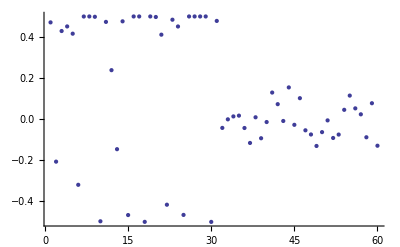

```mathematica
ListPlot[Zvals[mps]]
```

```mathematica
Chop[interactionsL[31],10^(-7)][[1]]
Chop[interactionsR[31],10^(-7)][[1]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
(a=With[{site=31},MPSEffectiveHam[interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]]
])//Chop//MatrixForm
```

(0.0956271 | 0.016845+0.015817 ⅈ | -0.0269972+0.0633363 ⅈ | -0.0219876+0.0102929 ⅈ | -0.0328988-0.116465 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.016845-0.015817 ⅈ | -0.151176 | -0.0760458+0.023087 ⅈ | -0.0830527+0.00694842 ⅈ | -0.043303+0.0680628 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0269972-0.0633363 ⅈ | -0.0760458-0.023087 ⅈ | 0.00765171 | -0.0841888-0.0900002 ⅈ | 0.0527058-0.0670596 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0219876-0.0102929 ⅈ | -0.0830527-0.00694842 ⅈ | -0.0841888+0.0900002 ⅈ | 0.0975526 | 0.0256639-0.000942617 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0328988+0.116465 ⅈ | -0.043303-0.0680628 ⅈ | 0.0527058+0.0670596 ⅈ | 0.0256639+0.000942617 ⅈ | -0.11811 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0956271 | 0.016845+0.015817 ⅈ | -0.0269972+0.0633363 ⅈ | -0.0219876+0.0102929 ⅈ | -0.0328988-0.116465 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.016845-0.015817 ⅈ | -0.151176 | -0.0760458+0.023087 ⅈ | -0.0830527+0.00694842 ⅈ | -0.043303+0.0680628 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.0269972-0.0633363 ⅈ | -0.0760458-0.023087 ⅈ | 0.00765171 | -0.0841888-0.0900002 ⅈ | 0.0527058-0.0670596 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.0219876-0.0102929 ⅈ | -0.0830527-0.00694842 ⅈ | -0.0841888+0.0900002 ⅈ | 0.0975526 | 0.0256639-0.000942617 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.0328988+0.116465 ⅈ | -0.043303-0.0680628 ⅈ | 0.0527058+0.0670596 ⅈ | 0.0256639+0.000942617 ⅈ | -0.11811 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0956271 | 0.016845+0.015817 ⅈ | -0.0269972+0.0633363 ⅈ | -0.0219876+0.0102929 ⅈ | -0.0328988-0.116465 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.016845-0.015817 ⅈ | -0.151176 | -0.0760458+0.023087 ⅈ | -0.0830527+0.00694842 ⅈ | -0.043303+0.0680628 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0269972-0.0633363 ⅈ | -0.0760458-0.023087 ⅈ | 0.00765171 | -0.0841888-0.0900002 ⅈ | 0.0527058-0.0670596 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0219876-0.0102929 ⅈ | -0.0830527-0.00694842 ⅈ | -0.0841888+0.0900002 ⅈ | 0.0975526 | 0.0256639-0.000942617 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0328988+0.116465 ⅈ | -0.043303-0.0680628 ⅈ | 0.0527058+0.0670596 ⅈ | 0.0256639+0.000942617 ⅈ | -0.11811 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0956271 | 0.016845+0.015817 ⅈ | -0.0269972+0.0633363 ⅈ | -0.0219876+0.0102929 ⅈ | -0.0328988-0.116465 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.016845-0.015817 ⅈ | -0.151176 | -0.0760458+0.023087 ⅈ | -0.0830527+0.00694842 ⅈ | -0.043303+0.0680628 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0269972-0.0633363 ⅈ | -0.0760458-0.023087 ⅈ | 0.00765171 | -0.0841888-0.0900002 ⅈ | 0.0527058-0.0670596 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0219876-0.0102929 ⅈ | -0.0830527-0.00694842 ⅈ | -0.0841888+0.0900002 ⅈ | 0.0975526 | 0.0256639-0.000942617 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0328988+0.116465 ⅈ | -0.043303-0.0680628 ⅈ | 0.0527058+0.0670596 ⅈ | 0.0256639+0.000942617 ⅈ | -0.11811 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0956271 | 0.016845+0.015817 ⅈ | -0.0269972+0.0633363 ⅈ | -0.0219876+0.0102929 ⅈ | -0.0328988-0.116465 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.016845-0.015817 ⅈ | -0.151176 | -0.0760458+0.023087 ⅈ | -0.0830527+0.00694842 ⅈ | -0.043303+0.0680628 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0269972-0.0633363 ⅈ | -0.0760458-0.023087 ⅈ | 0.00765171 | -0.0841888-0.0900002 ⅈ | 0.0527058-0.0670596 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0219876-0.0102929 ⅈ | -0.0830527-0.00694842 ⅈ | -0.0841888+0.0900002 ⅈ | 0.0975526 | 0.0256639-0.000942617 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0328988+0.116465 ⅈ | -0.043303-0.0680628 ⅈ | 0.0527058+0.0670596 ⅈ | 0.0256639+0.000942617 ⅈ | -0.11811 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0956271 | -0.016845-0.015817 ⅈ | 0.0269972-0.0633363 ⅈ | 0.0219876-0.0102929 ⅈ | 0.0328988+0.116465 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.016845+0.015817 ⅈ | 0.151176 | 0.0760458-0.023087 ⅈ | 0.0830527-0.00694842 ⅈ | 0.043303-0.0680628 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0269972+0.0633363 ⅈ | 0.0760458+0.023087 ⅈ | -0.00765171 | 0.0841888+0.0900002 ⅈ | -0.0527058+0.0670596 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0219876+0.0102929 ⅈ | 0.0830527+0.00694842 ⅈ | 0.0841888-0.0900002 ⅈ | -0.0975526 | -0.0256639+0.000942617 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0328988-0.116465 ⅈ | 0.043303+0.0680628 ⅈ | -0.0527058-0.0670596 ⅈ | -0.0256639-0.000942617 ⅈ | 0.11811 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0956271 | -0.016845-0.015817 ⅈ | 0.0269972-0.0633363 ⅈ | 0.0219876-0.0102929 ⅈ | 0.0328988+0.116465 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.016845+0.015817 ⅈ | 0.151176 | 0.0760458-0.023087 ⅈ | 0.0830527-0.00694842 ⅈ | 0.043303-0.0680628 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0269972+0.0633363 ⅈ | 0.0760458+0.023087 ⅈ | -0.00765171 | 0.0841888+0.0900002 ⅈ | -0.0527058+0.0670596 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0219876+0.0102929 ⅈ | 0.0830527+0.00694842 ⅈ | 0.0841888-0.0900002 ⅈ | -0.0975526 | -0.0256639+0.000942617 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0328988-0.116465 ⅈ | 0.043303+0.0680628 ⅈ | -0.0527058-0.0670596 ⅈ | -0.0256639-0.000942617 ⅈ | 0.11811 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0956271 | -0.016845-0.015817 ⅈ | 0.0269972-0.0633363 ⅈ | 0.0219876-0.0102929 ⅈ | 0.0328988+0.116465 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.016845+0.015817 ⅈ | 0.151176 | 0.0760458-0.023087 ⅈ | 0.0830527-0.00694842 ⅈ | 0.043303-0.0680628 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0269972+0.0633363 ⅈ | 0.0760458+0.023087 ⅈ | -0.00765171 | 0.0841888+0.0900002 ⅈ | -0.0527058+0.0670596 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0219876+0.0102929 ⅈ | 0.0830527+0.00694842 ⅈ | 0.0841888-0.0900002 ⅈ | -0.0975526 | -0.0256639+0.000942617 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0328988-0.116465 ⅈ | 0.043303+0.0680628 ⅈ | -0.0527058-0.0670596 ⅈ | -0.0256639-0.000942617 ⅈ | 0.11811 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0956271 | -0.016845-0.015817 ⅈ | 0.0269972-0.0633363 ⅈ | 0.0219876-0.0102929 ⅈ | 0.0328988+0.116465 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.016845+0.015817 ⅈ | 0.151176 | 0.0760458-0.023087 ⅈ | 0.0830527-0.00694842 ⅈ | 0.043303-0.0680628 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0269972+0.0633363 ⅈ | 0.0760458+0.023087 ⅈ | -0.00765171 | 0.0841888+0.0900002 ⅈ | -0.0527058+0.0670596 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0219876+0.0102929 ⅈ | 0.0830527+0.00694842 ⅈ | 0.0841888-0.0900002 ⅈ | -0.0975526 | -0.0256639+0.000942617 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0328988-0.116465 ⅈ | 0.043303+0.0680628 ⅈ | -0.0527058-0.0670596 ⅈ | -0.0256639-0.000942617 ⅈ | 0.11811 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0956271 | -0.016845-0.015817 ⅈ | 0.0269972-0.0633363 ⅈ | 0.0219876-0.0102929 ⅈ | 0.0328988+0.116465 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.016845+0.015817 ⅈ | 0.151176 | 0.0760458-0.023087 ⅈ | 0.0830527-0.00694842 ⅈ | 0.043303-0.0680628 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0269972+0.0633363 ⅈ | 0.0760458+0.023087 ⅈ | -0.00765171 | 0.0841888+0.0900002 ⅈ | -0.0527058+0.0670596 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0219876+0.0102929 ⅈ | 0.0830527+0.00694842 ⅈ | 0.0841888-0.0900002 ⅈ | -0.0975526 | -0.0256639+0.000942617 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0328988-0.116465 ⅈ | 0.043303+0.0680628 ⅈ | -0.0527058-0.0670596 ⅈ | -0.0256639-0.000942617 ⅈ | 0.11811)

```mathematica
operatorsR[32][[1,1]]
operatorsR[33][[1,1]]
```

{{0.180392+0. ⅈ,-0.0404013+0.121922 ⅈ,0.0459292+0.0424581 ⅈ,-0.0882347+0.0784901 ⅈ,-0.350566-0.115216 ⅈ},{-0.0404013-0.121922 ⅈ,-0.0254208+6.93889×10^-18 ⅈ,0.0417004+0.0967369 ⅈ,-0.230037+0.030717 ⅈ,-0.00964974+0.0197942 ⅈ},{0.0459292-0.0424581 ⅈ,0.0417004-0.0967369 ⅈ,0.369595-2.08167×10^-17 ⅈ,-0.169929-0.0685673 ⅈ,0.0786723+0.0162129 ⅈ},{-0.0882347-0.0784901 ⅈ,-0.230037-0.030717 ⅈ,-0.169929+0.0685673 ⅈ,-0.202348+4.16334×10^-17 ⅈ,0.0215366+0.0731868 ⅈ},{-0.350566+0.115216 ⅈ,-0.00964974-0.0197942 ⅈ,0.0786723-0.0162129 ⅈ,0.0215366-0.0731868 ⅈ,-0.0536857+6.93889×10^-18 ⅈ}}

{{-0.017466-1.04083×10^-17 ⅈ,-0.133215-0.254656 ⅈ,0.226413+0.0332747 ⅈ,-0.00197+0.000658454 ⅈ,-0.0457816-0.00239292 ⅈ},{-0.133215+0.254656 ⅈ,-0.0560381+1.38778×10^-17 ⅈ,-0.284134-0.02271 ⅈ,0.0100182-0.0222851 ⅈ,-0.00575154-0.0565453 ⅈ},{0.226413-0.0332747 ⅈ,-0.284134+0.02271 ⅈ,-0.0332686-1.04083×10^-17 ⅈ,-0.0259442+0.0759924 ⅈ,0.0227822-0.157462 ⅈ},{-0.00197-0.000658454 ⅈ,0.0100182+0.0222851 ⅈ,-0.0259442-0.0759924 ⅈ,-0.0543224+0. ⅈ,-0.206504-0.0198774 ⅈ},{-0.0457816+0.00239292 ⅈ,-0.00575154+0.0565453 ⅈ,0.0227822+0.157462 ⅈ,-0.206504+0.0198774 ⅈ,0.0663842-1.38778×10^-17 ⅈ}}

```mathematica
Chop[interactionsR[32][[3]]]
Chop[interactionsR[36][[3]]]
```

{{-0.0497892,-0.0304106-0.0454203 ⅈ,-0.093529-0.0139251 ⅈ,-0.0380764-0.0243556 ⅈ,-0.0155374-0.080227 ⅈ},{-0.0304106+0.0454203 ⅈ,-0.0443138,-0.0962092-0.0239023 ⅈ,-0.0778064-0.00271477 ⅈ,0.0565053+0.0434236 ⅈ},{-0.093529+0.0139251 ⅈ,-0.0962092+0.0239023 ⅈ,0.140336,0.112596-0.0452722 ⅈ,-0.0465366-0.0809951 ⅈ},{-0.0380764+0.0243556 ⅈ,-0.0778064+0.00271477 ⅈ,0.112596+0.0452722 ⅈ,0.0392707,0.0288636+0.0155865 ⅈ},{-0.0155374+0.080227 ⅈ,0.0565053-0.0434236 ⅈ,-0.0465366+0.0809951 ⅈ,0.0288636-0.0155865 ⅈ,0.101429}}

{{0.191613,0.00998531-0.00742168 ⅈ,-0.0996466-0.0353952 ⅈ,-0.00310641+0.0444039 ⅈ,0.0166125-0.0498177 ⅈ},{0.00998531+0.00742168 ⅈ,0.208567,0.0705296+0.081451 ⅈ,-0.0888764-0.0497528 ⅈ,0.0492427-0.0582218 ⅈ},{-0.0996466+0.0353952 ⅈ,0.0705296-0.081451 ⅈ,0.0826533,-0.0728367+0.189634 ⅈ,0.0346673-0.0818526 ⅈ},{-0.00310641-0.0444039 ⅈ,-0.0888764+0.0497528 ⅈ,-0.0728367-0.189634 ⅈ,0.0473211,0.0261674+0.0966375 ⅈ},{0.0166125+0.0498177 ⅈ,0.0492427+0.0582218 ⅈ,0.0346673+0.0818526 ⅈ,0.0261674-0.0966375 ⅈ,0.142097}}

```mathematica
canon
```

{{1.+0. ⅈ}}

### 60

```mathematica
MPSCanonizationCheck[mps,Site->60]
```

True

```mathematica
defineRight[1];
canon={{1.}};
```

```mathematica
With[{site=60},
{energy,new,info}=FindGroundMPSSite[mps[[site]].canon,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]];
]
```

```mathematica
mps[[60]]
```

{{{-1.+3.28202×10^-15 ⅈ},{0.+0. ⅈ}},{{3.60822×10^-16+9.50848×10^-16 ⅈ},{0.+0. ⅈ}}}

```mathematica
new
```

{{{-1.+3.28202×10^-15 ⅈ},{0.+0. ⅈ}},{{3.60822×10^-16+9.50848×10^-16 ⅈ},{0.+0. ⅈ}}}

```mathematica
With[{site=60},
(H60=MPSEffectiveHam[interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]])]//MatrixForm
```

(-53.5274+1.61762×10^-14 ⅈ | -4.49823×10^-16-1.44572×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-4.49823×10^-16+1.44572×10^-16 ⅈ | -53.3683+1.48644×10^-14 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -49.827+1.50435×10^-14 ⅈ | 8.12923×10^-15+2.43507×10^-15 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 8.12923×10^-15-2.43507×10^-15 ⅈ | -53.1679+1.61557×10^-14 ⅈ)

```mathematica
Chop[H60.Flatten[mps[[60]]]/(-53.527416598821944)-Flatten[mps[[60]]]]
```

{0,0,0,0}

```mathematica
canon
```

{{1.}}

```mathematica
With[{site=60},mps[[site]]=MPSCanonizeSite[new,canon,UseMatrix->False];
If[monitorenergy,energyList=energyList~Join~{{energy,info}}];]
```

### ** ** ** ** ** ** ** ***

```mathematica
With[{site=59},
{energy,new,info}=FindGroundMPSSite[mps[[site]].canon,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]];
energy
]
```

-53.5274

```mathematica
mps[[59]]
```

{{{-2.39627×10^-16-1.75126×10^-17 ⅈ,-0.00664008-0.000485274 ⅈ},{1.38477×10^-15+2.15139×10^-15 ⅈ,-0.277669-0.960503 ⅈ},{4.48925×10^-17-3.46276×10^-17 ⅈ,-0.0162083-0.00136837 ⅈ},{-1.30387×10^-18+4.86278×10^-20 ⅈ,0.000284896+0.000241998 ⅈ}},{{0.511217+0.859452 ⅈ,6.12357×10^-16+2.50161×10^-15 ⅈ},{-2.71056×10^-15-6.64655×10^-16 ⅈ,2.48232×10^-14-8.14822×10^-14 ⅈ},{-2.64567×10^-14+9.29908×10^-15 ⅈ,3.43768×10^-6+1.29553×10^-7 ⅈ},{4.20744×10^-15-1.64921×10^-15 ⅈ,-0.0039389-0.00294262 ⅈ}}}

```mathematica
new
```

{{{-2.39627×10^-16-1.75126×10^-17 ⅈ,0.+0. ⅈ},{1.38477×10^-15+2.15139×10^-15 ⅈ,0.+0. ⅈ},{4.48925×10^-17-3.46276×10^-17 ⅈ,0.+0. ⅈ},{-1.30387×10^-18+4.86278×10^-20 ⅈ,0.+0. ⅈ}},{{0.511217+0.859452 ⅈ,0.+0. ⅈ},{-2.71056×10^-15-6.64655×10^-16 ⅈ,0.+0. ⅈ},{-2.64567×10^-14+9.29908×10^-15 ⅈ,0.+0. ⅈ},{4.20744×10^-15-1.64921×10^-15 ⅈ,0.+0. ⅈ}}}

```mathematica
Total[Abs[mps[[59]]-new],Infinity]
```

1.02805

```mathematica
energy
```

-53.5274

```mathematica
With[{site=59},
(H59=MPSEffectiveHam[interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]])]//MatrixForm
```

(-51.327+1.48424×10^-14 ⅈ | -1.0809×10^-16+2.84841×10^-16 ⅈ | -4.08447×10^-15-4.08251×10^-15 ⅈ | 1.30287×10^-30-5.79927×10^-31 ⅈ | 1.74508×10^-13+6.04094×10^-13 ⅈ | 5.16035×10^-30+7.35425×10^-30 ⅈ | -2.42361×10^-14-1.68352×10^-13 ⅈ | -4.76383×10^-30-2.15712×10^-30 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.0809×10^-16-2.84841×10^-16 ⅈ | -51.6265+1.50503×10^-14 ⅈ | -5.90143×10^-31+1.29828×10^-30 ⅈ | -3.09683×10^-15-3.08707×10^-15 ⅈ | -8.74017×10^-30-2.07936×10^-30 ⅈ | 1.69547×10^-13+6.11404×10^-13 ⅈ | 4.99561×10^-30-1.54634×10^-30 ⅈ | -2.39149×10^-14-1.73484×10^-13 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-4.08447×10^-15+4.08251×10^-15 ⅈ | -5.90143×10^-31-1.29828×10^-30 ⅈ | -53.3765+1.53653×10^-14 ⅈ | 7.23215×10^-17-1.90583×10^-16 ⅈ | 1.52374×10^-9-1.86611×10^-8 ⅈ | 3.38296×10^-25+1.61801×10^-25 ⅈ | 2.42295×10^-10+3.74957×10^-10 ⅈ | -7.86645×10^-27+1.40095×10^-27 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
1.30287×10^-30+5.79927×10^-31 ⅈ | -3.09683×10^-15+3.08707×10^-15 ⅈ | 7.23215×10^-17+1.90583×10^-16 ⅈ | -53.1761+1.52318×10^-14 ⅈ | -3.60471×10^-25+1.03364×10^-25 ⅈ | 1.49301×10^-9-1.82937×10^-8 ⅈ | 4.95666×10^-27-6.26699×10^-27 ⅈ | 2.38263×10^-10+3.68214×10^-10 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
1.74508×10^-13-6.04095×10^-13 ⅈ | -8.74016×10^-30+2.07936×10^-30 ⅈ | 1.52374×10^-9+1.86611×10^-8 ⅈ | -3.60471×10^-25-1.03364×10^-25 ⅈ | -26.9838-2.30388×10^-15 ⅈ | -1.15443×10^-16+3.04218×10^-16 ⅈ | 0.357663-0.255201 ⅈ | -4.00422×10^-18-1.48834×10^-17 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
5.16035×10^-30-7.35425×10^-30 ⅈ | 1.69547×10^-13-6.11404×10^-13 ⅈ | 3.38296×10^-25-1.61801×10^-25 ⅈ | 1.49301×10^-9+1.82937×10^-8 ⅈ | -1.15443×10^-16-3.04218×10^-16 ⅈ | -27.3038-2.24859×10^-15 ⅈ | 1.28701×10^-17+8.48005×10^-18 ⅈ | 0.369949-0.264074 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-2.42361×10^-14+1.68352×10^-13 ⅈ | 4.99561×10^-30+1.54634×10^-30 ⅈ | 2.42295×10^-10-3.74957×10^-10 ⅈ | 4.95666×10^-27+6.26699×10^-27 ⅈ | 0.357663+0.255201 ⅈ | 1.28701×10^-17-8.48005×10^-18 ⅈ | -7.90204-6.76094×10^-15 ⅈ | 1.32257×10^-16-3.48527×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-4.76383×10^-30+2.15712×10^-30 ⅈ | -2.3915×10^-14+1.73484×10^-13 ⅈ | -7.86645×10^-27-1.40095×10^-27 ⅈ | 2.38263×10^-10-3.68214×10^-10 ⅈ | -4.00422×10^-18+1.48834×10^-17 ⅈ | 0.369949+0.264074 ⅈ | 1.32257×10^-16+3.48527×10^-16 ⅈ | -7.5355-6.83228×10^-15 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -53.5274+1.63693×10^-14 ⅈ | 1.3352×10^-15-3.51855×10^-15 ⅈ | 3.81685×10^-15+3.881×10^-15 ⅈ | 1.30287×10^-30-5.79927×10^-31 ⅈ | 1.35625×10^-13+6.6634×10^-13 ⅈ | 5.16035×10^-30+7.35425×10^-30 ⅈ | -2.41173×10^-14-2.03546×10^-13 ⅈ | -4.76383×10^-30-2.15712×10^-30 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.3352×10^-15+3.51855×10^-15 ⅈ | -49.827+1.65772×10^-14 ⅈ | -5.90143×10^-31+1.29828×10^-30 ⅈ | 4.8045×10^-15+4.87643×10^-15 ⅈ | -8.74017×10^-30-2.07936×10^-30 ⅈ | 1.30665×10^-13+6.7365×10^-13 ⅈ | 4.99561×10^-30-1.54634×10^-30 ⅈ | -2.37962×10^-14-2.08678×10^-13 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 3.81685×10^-15-3.881×10^-15 ⅈ | -5.90143×10^-31-1.29828×10^-30 ⅈ | -51.577+1.41666×10^-14 ⅈ | 1.51561×10^-15-3.99397×10^-15 ⅈ | 1.28582×10^-9-1.58187×10^-8 ⅈ | 3.38296×10^-25+1.61801×10^-25 ⅈ | 2.10483×10^-10+3.21743×10^-10 ⅈ | -7.86645×10^-27+1.40095×10^-27 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.30287×10^-30+5.79927×10^-31 ⅈ | 4.8045×10^-15-4.87643×10^-15 ⅈ | 1.51561×10^-15+3.99397×10^-15 ⅈ | -47.3765+1.4033×10^-14 ⅈ | -3.60471×10^-25+1.03364×10^-25 ⅈ | 1.2551×10^-9-1.54513×10^-8 ⅈ | 4.95666×10^-27-6.26699×10^-27 ⅈ | 2.06451×10^-10+3.15×10^-10 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.35625×10^-13-6.6634×10^-13 ⅈ | -8.74016×10^-30+2.07936×10^-30 ⅈ | 1.28582×10^-9+1.58187×10^-8 ⅈ | -3.60471×10^-25-1.03364×10^-25 ⅈ | -29.2104-1.91245×10^-15 ⅈ | 1.32785×10^-15-3.49917×10^-15 ⅈ | 0.439531-0.314067 ⅈ | -4.00422×10^-18-1.48834×10^-17 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 5.16035×10^-30-7.35425×10^-30 ⅈ | 1.30665×10^-13-6.7365×10^-13 ⅈ | 3.38296×10^-25-1.61801×10^-25 ⅈ | 1.2551×10^-9+1.54513×10^-8 ⅈ | 1.32785×10^-15+3.49917×10^-15 ⅈ | -25.5304-1.85715×10^-15 ⅈ | 1.28701×10^-17+8.48005×10^-18 ⅈ | 0.451816-0.32294 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.41173×10^-14+2.03546×10^-13 ⅈ | 4.99561×10^-30+1.54634×10^-30 ⅈ | 2.10483×10^-10-3.21743×10^-10 ⅈ | 4.95666×10^-27+6.26699×10^-27 ⅈ | 0.439531+0.314067 ⅈ | 1.28701×10^-17-8.48005×10^-18 ⅈ | -5.56091-7.19655×10^-15 ⅈ | 1.57555×10^-15-4.15192×10^-15 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -4.76383×10^-30+2.15712×10^-30 ⅈ | -2.37962×10^-14+2.08678×10^-13 ⅈ | -7.86645×10^-27-1.40095×10^-27 ⅈ | 2.06451×10^-10-3.15×10^-10 ⅈ | -4.00422×10^-18+1.48834×10^-17 ⅈ | 0.451816+0.32294 ⅈ | 1.57555×10^-15+4.15192×10^-15 ⅈ | -1.19437-7.26789×10^-15 ⅈ)

```mathematica
Chop[H59.Flatten[mps[[59]]]/energy-Flatten[mps[[59]]]]
```

{0,0.000235803+0.0000172331 ⅈ,0,0.00182237+0.00630388 ⅈ,0,0.00793744+0.000670113 ⅈ,0,-0.000139518-0.00011851 ⅈ,0,0,0,0,0,0.0000492029+1.00639×10^-6 ⅈ,0,0.00385098+0.00287694 ⅈ}

```mathematica
Chop[H59.Flatten[new]/energy-Flatten[new]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
canon
```

{{1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
tempA=mps[[59]]
```

{{{-2.39627×10^-16-1.75126×10^-17 ⅈ,-0.00664008-0.000485274 ⅈ},{1.38477×10^-15+2.15139×10^-15 ⅈ,-0.277669-0.960503 ⅈ},{4.48925×10^-17-3.46276×10^-17 ⅈ,-0.0162083-0.00136837 ⅈ},{-1.30387×10^-18+4.86278×10^-20 ⅈ,0.000284896+0.000241998 ⅈ}},{{0.511217+0.859452 ⅈ,6.12357×10^-16+2.50161×10^-15 ⅈ},{-2.71056×10^-15-6.64655×10^-16 ⅈ,2.48232×10^-14-8.14822×10^-14 ⅈ},{-2.64567×10^-14+9.29908×10^-15 ⅈ,3.43768×10^-6+1.29553×10^-7 ⅈ},{4.20744×10^-15-1.64921×10^-15 ⅈ,-0.0039389-0.00294262 ⅈ}}}

```mathematica
With[{site=59},mps[[site]]=MPSCanonizeSite[new,canon,UseMatrix->False];
If[monitorenergy,energyList=energyList~Join~{{energy,info}}];]
```

```mathematica
Total[Abs[mps[[59]]-tempA],Infinity]
```

4.02336

```mathematica
Chop[H59.Flatten[mps[[59]]]/energy-Flatten[mps[[59]]]]
```

{0,0,0.000129785-0.00281557 ⅈ,-2.60014×10^-10+2.23545×10^-10 ⅈ,3.49568×10^-10,-0.348546-0.344279 ⅈ,0,-0.00145018-0.00836678 ⅈ,0,0,0,0,0,-0.00844084+0.00603317 ⅈ,0,-0.977687}

```mathematica
Dimensions[mps[[59]]]
```

{2,4,2}

```mathematica
Dimensions[canon]
```

{4,4}

```mathematica
Chop[H59.Flatten[canon.#&/@mps[[59]]]/energy-Flatten[canon.#&/@mps[[59]]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
energy-(-53.527416598821944)
```

-7.10543×10^-15

```mathematica
prevEnergy=energy
```

-53.5274

### 58

```mathematica
With[{site=58},
{energy,new,info}=FindGroundMPSSite[mps[[site]].canon,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]];
energy
]
```

-53.5274

```mathematica
(energy-prevEnergy)/energy
```

2.65487×10^-16

```mathematica
Chop[mps[[58]].canon-new]
```

{{{0.22311-1.98752 ⅈ,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
Chop[canon]
```

{{1.,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Chop[Abs[mps[[59]]]]
```

{{{0,0},{1.,0},{0,1.},{0,0}},{{1.,0},{0,0},{0,0},{0,1.}}}

```mathematica
Chop[new]
```

{{{-0.111555+0.993758 ⅈ,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
With[{site=58},mps[[site]]=MPSCanonizeSite[new,canon,UseMatrix->False];
If[monitorenergy,energyList=energyList~Join~{{energy,info}}];]
```

```mathematica
Chop[canon]
```

{{1.,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

### 57

```mathematica
prevEnergy=energy
```

-53.5274

```mathematica
With[{site=57},
{energy,new,info}=FindGroundMPSSite[mps[[site]].canon,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]];
energy
]
```

-53.5274

```mathematica
(energy-prevEnergy)/energy
```

1.32744×10^-16

```mathematica
Chop[mps[[57]].canon-new]
```

{{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

```mathematica
Chop[canon]
```

{{1.,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
Chop[Abs[mps[[57]]]]
```

{{{1.,0,0,0,0},{0,0.0504077,0.75103,0.6086,0.170081},{0,0.00886717,0.178792,0.178465,0.133678},{0,0.0146596,0.216114,0.236746,0.0187287},{0,0.0392894,0.586592,0.699474,0.0899162}},{{0,0.997682,0.0454599,0.0444704,0.0195579},{0,0.0000173678,0.0000617448,0.000154166,0.00104424},{0,0.00122129,0.0147197,0.0406921,0.0533512},{0,0.0140147,0.102954,0.175635,0.882681},{0,0.0074358,0.0175574,0.134025,0.403002}}}

```mathematica
Chop[new]
```

{{{-0.101269+0.994859 ⅈ,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

```mathematica
With[{site=57},mps[[site]]=MPSCanonizeSite[new,canon,UseMatrix->False];
If[monitorenergy,energyList=energyList~Join~{{energy,info}}];]
```

```mathematica
Chop[canon]
```

{{1.,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

### 56

```mathematica
prevEnergy=energy
```

-53.5274

```mathematica
With[{site=56},
{energy,new,info}=FindGroundMPSSite[mps[[site]].canon,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]];
energy
]
```

-53.5274

```mathematica
(energy-prevEnergy)/energy
```

-1.32744×10^-16

```mathematica
Chop[mps[[56]].canon-new]
```

{{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

```mathematica
Chop[canon]
```

{{1.,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
Chop[Abs[mps[[56]]]]
```

{{{0,0.999958,0.00362486,0.00161479,0.000972181},{0,0.000144564,0.00272591,0.00595938,0.00483067},{0,0.000645637,0.0121851,0.0263127,0.0215697},{0,0.00705892,0.132905,0.290532,0.235607},{0,0.00161793,0.0303143,0.0662245,0.0534902}},{{1.,0,0,0,0},{0,0.000456209,0.115359,0.0155067,0.037358},{0,0.00448405,0.961253,0.0942192,0.15856},{0,0.0032268,0.203225,0.287641,0.881558},{0,0.000538854,0.0513116,0.904776,0.370753}}}

```mathematica
Chop[new]
```

{{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0.114386-0.993436 ⅈ,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

```mathematica
With[{site=56},mps[[site]]=MPSCanonizeSite[new,canon,UseMatrix->False];
If[monitorenergy,energyList=energyList~Join~{{energy,info}}];]
```

```mathematica
Chop[canon]
```

{{1.,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

### Old part

```mathematica
Do[
If[verbose,NotebookDelete[message];message=PrintTemporary["Left sweep:"<>ToString[sweep]<>", site:"<>ToString[site]<>", Energy:"<>ToString[energy]]];
success=False;
While[!success,
{energy,new,info}=FindGroundMPSSite[mps[[site]].canon,interactionsL[site-1],interactionsR[site+1],fieldL[site-1],fieldR[site+1],operatorsL[site-1],operatorsR[site+1],HMatrix[[All,Max[1,site-IntRange];;site,Max[1,site-IntRange];;Min[numTensors,site+IntRange]]]];
success=(IsLinkActive[]===1);
If[!success,Print["Fallen link..."];ClearLink[link];EstablishLink[link];Print["And we're back."]];
];
mps[[site]]=MPSCanonizeSite[new,canon,UseMatrix->False];
If[monitorenergy,energyList=energyList~Join~{{energy,info}}];
,{site,numTensors,1,-1}];


sweep+=0.5;
If[Abs[(energy-prevEnergy)/energy]<tol,stillconverging=False,prevEnergy=energy];






If[verbose,NotebookDelete[message]];
If[Total[Abs[#[[2]]]&/@energyList]>0,
Print["Arpack error reported:"];
Print[Cases[#[[2]]&/@energyList,Except[0]]]
];
ClearAll[energy,prevEnergy,sweeps,sweep,IntRange,monitorenergy,tol,L,R,fieldL,fieldR,operatorsR,operatorsL,interactionsL,interactionsR,Heff,numTensors,defineRight,defineLeft,χR,χL,new,canon,stillconverging,verbose,message,info,success];
#[[1]]&/@energyList
];
```

## Hand mps

```mathematica
mps=newmps;
```

```mathematica
one={{0,0},{1,0}};
two={{0,1},{0,0}};
zero={{0,0},{0,0}};
```

```mathematica
MPSCanonize[mps]
```

0

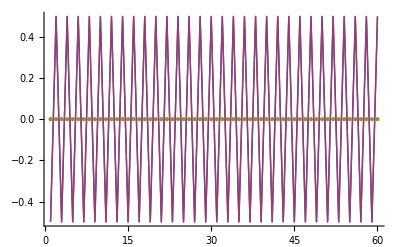

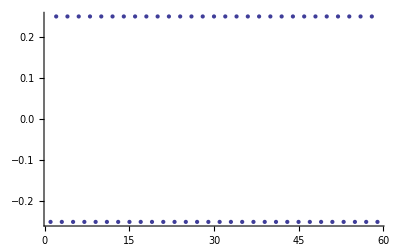

{-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25,0.25,-0.25}

```mathematica
mymps={{{{1,0}},{{0,1}}}}~Join~Table[If[EvenQ[n],{one,two},{one,two}],{n,1,58}]~Join~{{{{0},{1}},{{1},{0}}}};
ListPlot[{Zvals[newmps],Zvals[mps],Zvals[mymps]},Joined->{True,True,False}]
ListPlot[MPSCorrelation[mps,sigma[3],1,sigma[3],60]]
MPSCorrelation[mps,sigma[3],1,sigma[3],60]
```

```mathematica
one.Transpose[one]+two.Transpose[two]
```

{{1,0},{0,1}}

```mathematica
Transpose[one].one+Transpose[two].two
```

{{1,0},{0,1}}

```mathematica
LProduct[{{{0},{1}},{{1},{0}}},{{{0},{1}},{{1},{0}}}]
```

{{2}}

```mathematica
Dimensions[{{{1},{0}},{{1},{1}}}]
RProduct[{{{0},{1}},{{1},{0}}},{{{0},{1}},{{1},{0}}}]
```

{2,2,1}

{{1,0},{0,1}}

```mathematica
two.{{0},{1}}
```

{{1},{0}}

```mathematica
MPSCanonizationCheck[mymps]
```

True

```mathematica
mps=newmps;
```

```mathematica
MPSCanonize[mps]
```

0

```mathematica
mps=MPSExpandBond[mps,5];
```

Grow χ to 5

```mathematica
Manipulate[{Abs[Chop[mps[[n,1]],10^(-8)]]//MatrixForm,Abs[Chop[mps[[n,2]],10^(-8)]]//MatrixForm},{n,1,Length[mps],1}]
```

```mathematica
MPSCanonize[mps,Site->30]
```

30

```mathematica
MPSCanonize[mps,Site->n];
```

```mathematica
defineRight[1];
defineLeft[1];
```

```mathematica
Manipulate[
{Chop[L[n-1]]//MatrixForm,
Chop[R[n+1]]//MatrixForm},{n,1,60,1}]
```

```mathematica
defineRight[1];
defineLeft[1];
Chop[interactionsL[31],10^(-7)][[3]]//MatrixForm
Chop[interactionsR[30],10^(-7)][[3]]//MatrixForm
```

(-6.77061 | 0
0 | -6.77061)

(-6.77061 | 0
0 | -6.77061)

```mathematica
defineRight[1];
defineLeft[1];
MatrixForm/@Chop[operatorsL[31][[3]],10^(-7)]
MatrixForm/@Chop[operatorsR[30][[3]],10^(-7)]
```

{(0.5 | 0
0 | -0.5),(-0.5 | 0
0 | 0.5),(0.5 | 0
0 | -0.5),(-0.5 | 0
0 | 0.5),(0.5 | 0
0 | -0.5),(-0.5 | 0
0 | 0.5),(0.5 | 0
0 | -0.5),(-0.5 | 0
0 | 0.5)}

{(-0.5 | 0
0 | 0.5),(0.5 | 0
0 | -0.5),(-0.5 | 0
0 | 0.5),(0.5 | 0
0 | -0.5),(-0.5 | 0
0 | 0.5),(0.5 | 0
0 | -0.5),(-0.5 | 0
0 | 0.5),(0.5 | 0
0 | -0.5)}